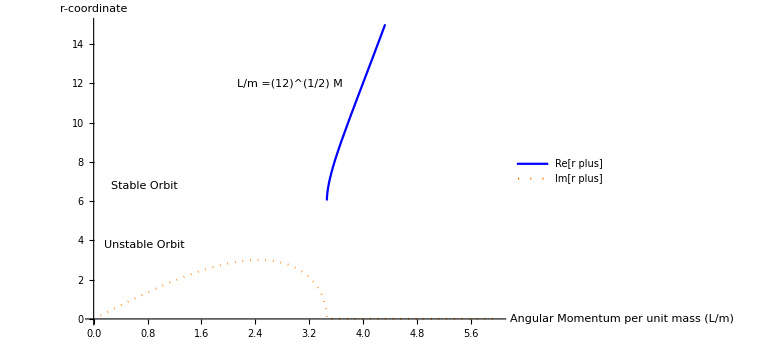

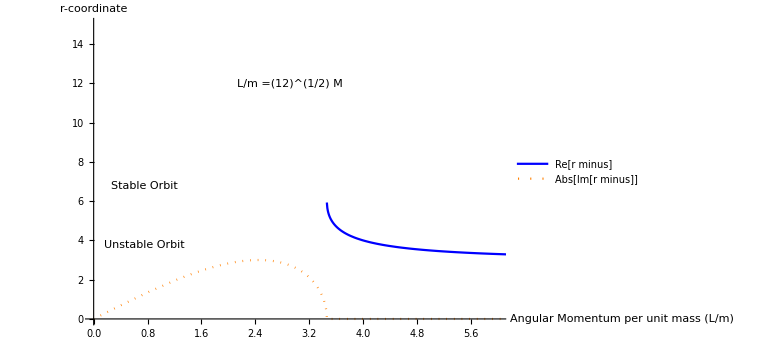

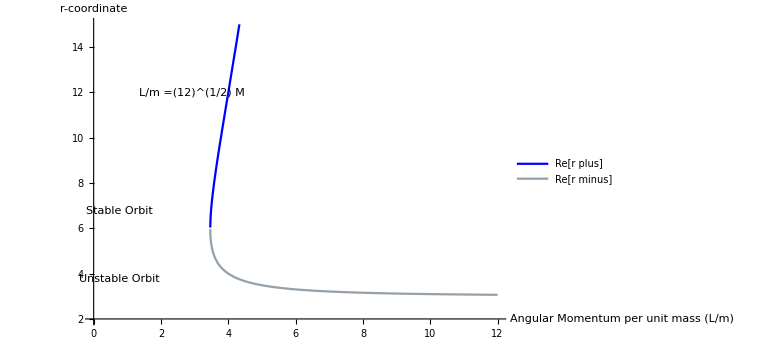

```mathematica
M=1;
rplus[l_]=(l^2/(2 M))*(1+Sqrt[1-(12 M^2/l^2)]);
rminus[l_]=(l^2/(2 M))*(1-Sqrt[1-(12 M^2/l^2)]);
plotCallouts={Inset[Framed[Style["Stable Orbit",10],Background->LightYellow],{0.75,6.75}],Inset[Framed[Style["Unstable Orbit",10],Background->LightYellow],{0.75,3.75}],Inset[Framed[Style["L/m =(12\!\(\*SuperscriptBox[\()\), \(1/2\)]\) M",10],Background->LightYellow],{(Sqrt[12]*M-0.55),12}]};

Plot[{rplus[l],Im[rplus[l]]},{l,0,6 M},AxesLabel->{"Angular Momentum per unit mass (L/m)","r-coordinate"},PlotLegends->{"Re[r plus]","Im[r plus]"},ImageSize->Large,Exclusions->None,GridLines->{{{Sqrt[12]*M,Dashed}},{{3 M,{Pink,Dashed}},{6 M,{Red,Dashed}}}},PlotStyle->{{Blue,Thick},{Orange,Dotted}},PlotRange->{{0,6 M},{0,15 M}},Epilog->plotCallouts]

Plot[{rminus[l],Abs[Im[rminus[l]]]},{l,0,20 M},AxesLabel->{"Angular Momentum per unit mass (L/m)","r-coordinate"},PlotLegends->{"Re[r minus]","Abs[Im[r minus]]"},ImageSize->Large,Exclusions->None,GridLines->{{{Sqrt[12]*M,Dashed}},{{3 M,{Pink,Dashed}},{6 M,{Red,Dashed}}}},PlotStyle->{{Blue,Thick},{Orange,Dotted}},PlotRange->{{0,6 M},{0,15 M}},Epilog->plotCallouts]

Plot[{rplus[l],rminus[l]},{l,2,12 M},AxesLabel->{"Angular Momentum per unit mass (L/m)","r-coordinate"},PlotLegends->{"Re[r plus]","Re[r minus]"},ImageSize->Large,Exclusions->None,GridLines->{{{Sqrt[12]*M,Dashed}},{{3 M,{Pink,Dashed}},{6 M,{Red,Dashed}}}},PlotStyle->{{Blue},{Darker[LightBlue]}},PlotRange->{{0,12 M},{2,15 M}},Epilog->plotCallouts]
V[r_] = Sqrt[(1-(2M)/r)×(1+(l/r)^2)];
```

```mathematica
Plot3D[Sqrt[(1-(2M)/r)×(1+(l/r)^2)], {r,0,20M},{l,3M,5M},
 ImageSize->Large, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[(1-(2M)/r)×(1+(l/r)^2), {r,0,20M},{l,3.5M,4M},
 ImageSize->Large, AxesLabel->{"Radius","Angular Momentum", "Effective Potential"}]
```

-Graphics3D-

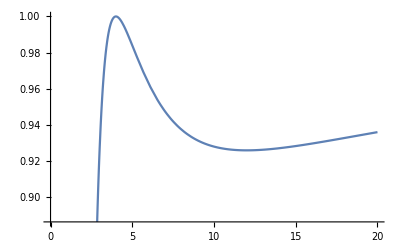

```mathematica
Plot[(1-(2M)/r)×(1+(4/r)^2), {r,0,20M}]
```

```mathematica
Plot3D[r^2-r*l^2+3 l^2, {r,0,20M},{l,0,5M},
 ImageSize->Large, AxesLabel->{"Radius","Angular Momentum", "Effective Potential"}]
```

-Graphics3D-